```mathematica
h:=-f √(Jx^3)(3Cos[ϕx+(δ s)/R+ν s/R]+(Cos[3(ϕx+(δ s)/R+ν s/R)]))+δ/R(Jx-Jy);
FullSimplify[-D[h,ϕx]];
FullSimplify[D[h,Jx]];
FullSimplify[-D[h,ϕy]];
FullSimplify[D[h,Jy]];
```

```mathematica
TrigReduce[Cos[(ν+δ+x)]^2Cos[(ν-δ+y)]^1]
```

1/4 (2 Cos[y-δ+ν]+Cos[2 x-y+3 δ+ν]+Cos[2 x+y+δ+3 ν])

```mathematica
TrigReduce[Cos[ν+δ+x]^3Cos[ν-δ+y]^0]
```

1/4 (3 Cos[x+δ+ν]+Cos[3 x+3 δ+3 ν])

```mathematica
hh=FullSimplify[h/.{ϕx->-(δ s)/R+Φ-ν}]
Φshtrich=FullSimplify[D[hh,Jx]]+2δ/R
Jxshtrich=FullSimplify[-D[hh,Φ]]
Jyshtrich=0; ϕyshtrich=-δ/R;
Simplify[Solve[f √((II-J) (II+J))+2 f1 (II-J) (II+J) Cos[Φ]==0,Cos[Φ]]];
Simplify[2(f/(2 f1 √(II^2-J^2)))^2-1];
FullSimplify[D[hh,II]];
```

((Jx-Jy) δ)/R-4 f √(Jx^3) Cos[Φ]^3

(3 δ)/R-(6 f √(Jx^3) Cos[Φ]^3)/Jx

-12 f √(Jx^3) Cos[Φ]^2 Sin[Φ]

```mathematica
((Jx-Jy) δ)/R-f √(Jx^3) Cos[Φ] (3+Cos[Φ]^2)/.{f->1,R->1,δ->0.1}
```

0.1 (Jx-Jy)-√(Jx^3) Cos[Φ] (3+Cos[Φ]^2)

```mathematica
Manipulate[ContourPlot[(((Jx-Jy) δ)/R-4 f √(Jx^3) Cos[Φ]^3)/.{Jy->man,f->1,R->1,δ->0.1},{Φ, -2π,0},{Jx, 0, 1}],{man,0,1}]
```

```mathematica
h:=-f √(Jx^3)(3Cos[ϕx+(δ s)/R+ν]+(Cos[ϕx+(δ s)/R+ν])^3)+δ/R(Jx-Jy);
```

```mathematica
Manipulate[ContourPlot[hh/.{II->1,f->.98, f1->f1a,R->2,p->1.7,q->-0,r->1.7,δ->0.2,J->Cos[(x^2+y^2) π/2],Cos[Φ]->x/Sqrt[(x^2+y^2)],Cos[2 Φ]->2x^2/(x^2+y^2)-1},{x, -1,1},{y, -1, 1},Contours->30],{f1a,0,1}]
```

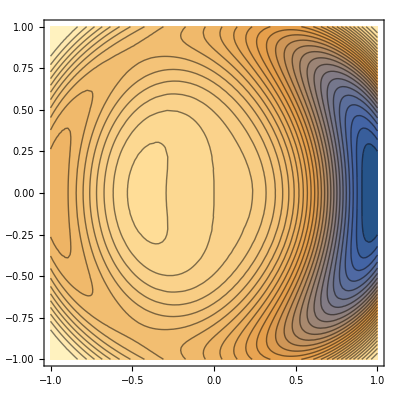

```mathematica
ContourPlot[hh/.{II->1,f->.98, f1->1,R->2,p->1.7,q->-0,r->1.7,δ->0.2,J->-Cos[(x^2+y^2) π/2],Cos[Φ]->x/Sqrt[(x^2+y^2)],Cos[2 Φ]->2x^2/(x^2+y^2)-1},{x, -1,1},{y, -1, 1},Contours->30]
```

```mathematica
sol=Flatten[Solve[Φshtrich==0/.{Cos[Φ]->-1,Cos[2Φ]->1},δ]]
sol1=Flatten[Solve[Φshtrich==0/.{Cos[Φ]->-f/(2 f1 √(II^2-J^2)),Cos[2Φ]->-1+f^2/(2 f1^2 (II^2-J^2))},δ]]
```

{δ→(-(f1 J)/2+(f J)/(2 √((II-J) (II+J)))-(II p)/4+(II r)/4-1/4 J (2 f1+p-2 q+r)) R}

{δ→-1/4 (II p+J p-2 J q-II r+J r) R}

```mathematica
soll=Flatten[Solve[Φshtrich==0/.{Cos[Φ]->1,Cos[2Φ]->1},J]];
```

```mathematica
Cos[1.37]
```

0.19945

```mathematica
Sin[1.37]
```

0.979908

```mathematica
solPlot=sol/.{II->II,f->0.2,f1->1,p->0.4,R->1,q->-.2,r->0.6}
Jplot={δ/.{solPlot[[1]]}(*,J/.{solPlot[[2]]},J/.{solPlot[[3]]},J/.{solPlot[[4]]}*)};

solPlot1=sol1/.{II->II,f->0.2,f1->1,p->0.4,R->1,q->-.2,r->0.6}
Jplot1={δ/.{solPlot1[[1]]}};

(*sollPlot=soll/.{II->1,f->0.2,f1->1,R->1,q->-.2,r->0.6};*)
(*Jplotl={J/.{sollPlot[[1]]},J/.{sollPlot[[2]]},J/.{sollPlot[[3]]},J/.{sollPlot[[4]]}};*)

Manipulate[Plot[{Jplot/.{II->f1a},Jplot1/.{II->f1a}},{J,-1,1}(*,PlotRange->{-1,1}*)],{f1a,0.00001,1}]
```

{δ→0.05 II-1.35 J+(0.1 J)/(√((II-J) (II+J)))}

{δ→1/4 (0.2 II-1.4 J)}

```mathematica
Jplot/.{δ->-0.7}
```

{-0.998867-2.06595×10^-19 ⅈ,0.536878+1.34627×10^-17 ⅈ,0.649347-1.67795×10^-17 ⅈ,0.982453+3.52331×10^-18 ⅈ}

```mathematica
plotFase=-f/(2 f1 √(II^2-J^2))/.{J->(-II p R+II r R-4 δ)/((p-2 q+r) R)};
```

```mathematica
Manipulate[Plot[plotFase/.{II->1,f->0.2, f1->f1a,R->1,p->0.3,q->-.2,r->0.6},{δ,-1,1},PlotRange->{-1,1}],{f1a,0.01,1}]
```

```mathematica
sol1=sol/.{II->1,f->-0.2,δ->-0.04,R->1,p->-0.02,q->-0.5,r->0.02}
```

{J→-0.943957-9.33782×10^-19 ⅈ,J→0.142438+1.47905×10^-17 ⅈ,J→0.348935-1.75238×10^-17 ⅈ,J→0.852584+3.66707×10^-18 ⅈ}

```mathematica
sol2=sol/.{II->1,f->-0.2,δ->0.09,R->1,p->-0.5,q->-0.02,r->0.5}
```

{J→-0.860094,J→0.834837,J→16.0126-10.0061 ⅈ,J→16.0126+10.0061 ⅈ}

```mathematica
ΦΦ=FullSimplify[D[hh,{Φ,2}]]
```

1/2 f √((II-J) (II+J)) Cos[Φ]+f1 (II-J) (II+J) Cos[2 Φ]

```mathematica
JJ = FullSimplify[D[hh,{J,2}]]
```

1/4 (2 f1+p-2 q+r+(2 f II^2 Cos[Φ])/((II-J) (II+J))^(3/2)+2 f1 Cos[2 Φ])

```mathematica
ΦJ=FullSimplify[D[D[hh,Φ],J]]
```

-(f J Sin[Φ])/(2 √((II-J) (II+J)))-f1 J Sin[2 Φ]

```mathematica
ΦΦ/.{Φ->π,sol1[[4]],II->1,f->-0.2,δ->0.09,R->1,p->-0.02,q->-0.02,r->0.02}
```

0.0756148

```mathematica
JJ/.{Φ->π,sol1[[4]],II->1,f->-0.2,δ->0.09,R->1,p->-0.02,q->-0.02,r->0.02}
```

0.241302

```mathematica
ΦΦ/.{Φ->π,sol2[[2]],II->1,f->-0.2,δ->0.09,R->1,p->-0.02,q->-0.02,r->0.02}
```

0.0550497

```mathematica
JJ/.{Φ->π,sol2[[2]],II->1,f->-0.2,δ->0.09,R->1,p->-0.02,q->-0.02,r->0.02}
```

0.609426

```mathematica
_____________---------------------_______without xy_________----------------------__________________
```

```mathematica
h:=δ/R(Ja-Jb)+1/2(p Ja^2+2 q Ja Jb+r Jb^2)-f1 Ja Jb (1+Cos[2ϕa-2ϕb+4 δ/R])
```

```mathematica
FullSimplify[-D[h,ϕa]]
```

-2 f1 Ja Jb Sin[(4 δ)/R+2 ϕa-2 ϕb]

```mathematica
FullSimplify[D[h,Ja]]
```

-f1 Jb+Ja p+Jb q+δ/R-f1 Jb Cos[(4 δ)/R+2 ϕa-2 ϕb]

```mathematica
FullSimplify[-D[h,ϕb]]
```

2 f1 Ja Jb Sin[(4 δ)/R+2 ϕa-2 ϕb]

```mathematica
FullSimplify[D[h,Jb]]
```

-f1 Ja+Ja q+Jb r-δ/R-f1 Ja Cos[(4 δ)/R+2 ϕa-2 ϕb]

```mathematica
hh=FullSimplify[h/.{Ja->(II+J)/2,Jb->(II-J)/2,ϕa->ϕb-(2 δ)/R+Φ}]
```

(2 f1 (-II^2+J^2) R+(II+J) ((II+J) p+2 (II-J) q) R+(II-J)^2 r R+8 J δ+2 f1 (-II^2+J^2) R Cos[2 Φ])/(8 R)

```mathematica
Jshtrich=FullSimplify[-D[hh,Φ]]
```

f1 (-II^2+J^2) Cos[Φ] Sin[Φ]

```mathematica
Φshtrich=FullSimplify[D[hh,J]]
```

(II (p-r) R+J (2 f1+p-2 q+r) R+4 δ+2 f1 J R Cos[2 Φ])/(4 R)

```mathematica
FullSimplify[D[hh,II]]
```

1/4 (-2 f1 II+J (p-r)+II (p+2 q+r)-2 f1 II Cos[2 Φ])

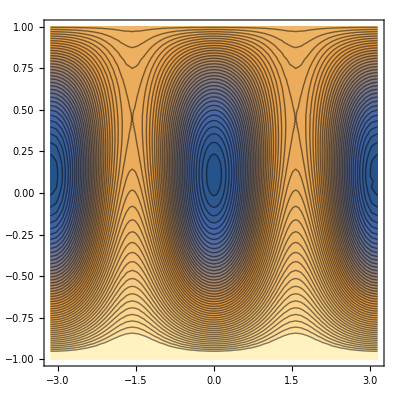

```mathematica
ContourPlot[hh/.{II->1,f->0.2, f1->1,R->1,p->0.3,q->-.2,r->0.6, δ->-0.07},{Φ, -π,π},{J, -1, 1},Contours->50]
```

```mathematica
sol=Flatten[Solve[Φshtrich==0/.{Cos[2Φ]->1},J]]
sol1=Flatten[Solve[Φshtrich==0/.{Cos[2Φ]->-1},J]]
```

{J→(-II p R+II r R-4 δ)/((4 f1+p-2 q+r) R)}

{J→(-II p R+II r R-4 δ)/((p-2 q+r) R)}

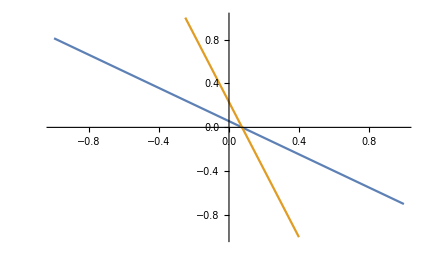

```mathematica
solPlot=sol/.{II->1,f->0.2, f1->1,R->1,p->0.3,q->-.2,r->0.6};
solPlot1=sol1/.{II->1,f->0.2, f1->1,R->1,p->0.3,q->-.2,r->0.6};
Jplot={J/.{solPlot[[1]]}};
Jplot1={J/.{solPlot1[[1]]}};
Plot[{Jplot,Jplot1},{δ,-1,1},PlotRange->{-1,1}]
```

```mathematica
Jplot/.{δ->0.075}
```

{0.}

```mathematica
sol1=sol/.{II->1,f->-0.2,δ->-0.04,R->1,p->-0.02,q->-0.5,r->0.02}
```

{J→0.2/(1.+4 f1)}

```mathematica
sol2=sol/.{II->1,f->-0.2,δ->0.09,R->1,p->-0.5,q->-0.02,r->0.5}
```

{J→0.64/(0.04+4 f1)}

```mathematica
_____________---------------------_______without p,q, r-------------------__________________
```

```mathematica
hh=Simplify[1/(8 R)(2 f1 (-II^2+J^2) R+8 J δ-4 f √((II-J) (II+J)) R Cos[Φ]+2 f1 (-II^2+J^2) R Cos[2 Φ])]
```

1/4 (f1 (-II^2+J^2)+(4 J δ)/R-2 f √(II^2-J^2) Cos[Φ]+f1 (-II^2+J^2) Cos[2 Φ])

```mathematica
Jshtrich=FullSimplify[-D[hh,Φ]]
```

-1/2 (f √((II-J) (II+J))+2 f1 (II-J) (II+J) Cos[Φ]) Sin[Φ]

```mathematica
Φshtrich=FullSimplify[D[hh,J]]
```

1/2 (f1 J+(2 δ)/R+(f J Cos[Φ])/(√((II-J) (II+J)))+f1 J Cos[2 Φ])

```mathematica
FullSimplify[D[hh,II]]
```

1/2 II Cos[Φ] (-f/(√((II-J) (II+J)))-2 f1 Cos[Φ])

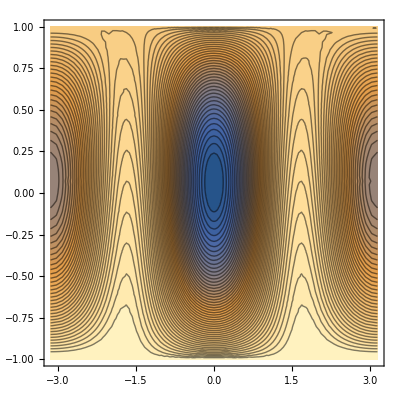

```mathematica
ContourPlot[hh/.{II->1,f->0.2, f1->1,R->1,p->0.3,q->-.2,r->0.6, δ->-0.07},{Φ, -π,π},{J, -1, 1},Contours->50]
```

```mathematica
sol=Flatten[Solve[Φshtrich==0/.{Cos[Φ]->-1,Cos[2Φ]->1},δ]]
sol1=Flatten[Solve[Φshtrich==0/.{Cos[Φ]->-f/(2 f1 √(II^2-J^2)),Cos[2Φ]->-1+f^2/(2 f1^2 (II^2-J^2))},δ]]
```

{δ→-((-f J+2 f1 J √(II^2-J^2)) R)/(2 √(II^2-J^2))}

{δ→0}

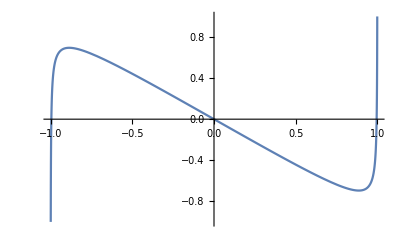

```mathematica
solPlot=sol/.{II->1,f->0.2, f1->1,R->1,p->0.3,q->-.2,r->0.6};
solPlot1=sol1/.{II->1,f->0.2, f1->1,R->1,p->0.3,q->-.2,r->0.6};
Jplot={δ/.{solPlot[[1]]}};
Plot[{Jplot,Jplot1},{J,-1,1},PlotRange->{-1,1}]
```

```mathematica
Jplot/.{δ->-0.7}
```

{0.584906}

```mathematica
sol1=sol/.{II->1,f->-0.2,δ->-0.04,R->1,p->-0.02,q->-0.5,r->0.02}
```

{J→0.2/(1.+4 f1)}

```mathematica
sol2=sol/.{II->1,f->-0.2,δ->0.09,R->1,p->-0.5,q->-0.02,r->0.5}
```

{J→0.64/(0.04+4 f1)}

```mathematica
►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►
►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►
```

```mathematica
-1/2 (η Sin[Θ] √((II-J[t]) (II+J[t]))+2 f1 (II-J[t]) (II+J[t]) Cos[Φ[t]]) Sin[Φ[t]]_Jstr_sum
1/4 (II p-II r+J[t] (2 f1+p-2 q+r)+(4 η Cos[Θ])/R+(2 η Sin[Θ] J[t] Cos[Φ[t]])/(√((II-J[t]) (II+J[t])))+2 f1 J[t] Cos[2 Φ[t]])_Φstr_sum
f1 (-II^2+J[t]^2) Cos[Φ[t]] Sin[Φ[t]]_Jstr_Without_xy
(II (p-r) R+J[t](2 f1+p-2 q+r) R+4 η Cos[Θ]+2 f1 J[t] R Cos[2 Φ[t]])/(4 R)_Φstr_Without_xy
-1/2 (η Sin[Θ] √((II-J[t]) (II+J[t]))+2 f1 (II-J[t]) (II+J[t]) Cos[Φ[t]]) Sin[Φ[t]]_Jstr_Without_pqr
1/2 (f1 J[t]+(2 η Cos[Θ])/R+(η Sin[Θ] J[t] Cos[Φ[t]])/(√((II-J[t]) (II+J[t])))+f1 J[t] Cos[2 Φ[t]])_Φstr_Without_pqr
```

```mathematica
JStr=-1/2 (η Sin[Θ] √((II-J[t]) (II+J[t]))+2 f1 (II-J[t]) (II+J[t]) Cos[Φ[t]]) Sin[Φ[t]]/.{II->1,η->1,Θ->1.37 ,R->2,p->1.7,q->0,r->1.7,f1->1};
ΦStr=1/4 (II p-II r+J[t] (2 f1+p-2 q+r)+(4 η Cos[Θ])/R+(2 η Sin[Θ] J[t] Cos[Φ[t]])/(√((II-J[t]) (II+J[t])))+2 f1 J[t] Cos[2 Φ[t]])/.{II->1,η->1,Θ->1.37 ,R->2,p->1.7,q->0,r->1.7, f1->1};

(*"nach.uslov."*)

plot2=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==-.95,Φ[0]==0},{J[t],Φ[t]},{t,0,180}];
P2=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot2],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black,AxesLabel->{x,y,z}];
plot3=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==-.9,Φ[0]==0},{J[t],Φ[t]},{t,0,180}];
P3=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot3],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black,AxesLabel->{x,y,z}];
plot4=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==-.8,Φ[0]==0.0},{J[t],Φ[t]},{t,0,180}];
P4=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot4],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black,AxesLabel->{x,y,z}];
plot5=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==-.6,Φ[0]==0.0},{J[t],Φ[t]},{t,0,180}];
P5=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot5],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black,AxesLabel->{x,y,z}];
plot6=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==-.3,Φ[0]==0.0},{J[t],Φ[t]},{t,0,180}];
P6=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot6],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black,AxesLabel->{x,y,z}];
plot7=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==0,Φ[0]==0},{J[t],Φ[t]},{t,0,180}];
P7=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot7],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black,AxesLabel->{x,y,z}];
plot8=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==.3,Φ[0]==0.0},{J[t],Φ[t]},{t,0,180}];
P8=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot8],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black,AxesLabel->{x,y,z}];
plot9=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==.6,Φ[0]==0},{J[t],Φ[t]},{t,0,180}];
P9=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot9],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black,AxesLabel->{x,y,z}];
plot10=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==.8,Φ[0]==0},{J[t],Φ[t]},{t,0,180}];
P10=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot10],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black,AxesLabel->{x,y,z}];
plot11=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==.9,Φ[0]==0.0},{J[t],Φ[t]},{t,0,180}];
P11=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot11],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black,AxesLabel->{x,y,z}];
plot12=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==.95,Φ[0]==0.0},{J[t],Φ[t]},{t,0,180}];
P12=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot12],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black,AxesLabel->{x,y,z}];
plot13=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==.99,Φ[0]==0},{J[t],Φ[t]},{t,0,180}];
P13=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot13],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black,AxesLabel->{x,y,z}];
plot20=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==.75,Φ[0]==.001+4π/3},{J[t],Φ[t]},{t,0,180}];
P20=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot20],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black,AxesLabel->{x,y,z}];
plot14=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==.3,Φ[0]==π},{J[t],Φ[t]},{t,0,180}];
P14=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot14],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black,AxesLabel->{x,y,z}];
plot15=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==.6,Φ[0]==π},{J[t],Φ[t]},{t,0,180}];
P15=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot15],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black,AxesLabel->{x,y,z}];
plot16=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==.8,Φ[0]==π},{J[t],Φ[t]},{t,0,180}];
P16=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot16],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black,AxesLabel->{x,y,z}];
plot17=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==.9,Φ[0]==π},{J[t],Φ[t]},{t,0,180}];
P17=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot17],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black,AxesLabel->{x,y,z}];
plot18=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==.95,Φ[0]==π},{J[t],Φ[t]},{t,0,180}];
P18=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot18],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black,AxesLabel->{x,y,z}];
plot19=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==.99,Φ[0]==π},{J[t],Φ[t]},{t,0,180}];
P19=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot19],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black,AxesLabel->{x,y,z}];

Show[{P2,P3,P4,P5,P6,P7,P8,P9,P10,P11,P12,P13,P14,P15,P16,P17,P18,P19,P20},PlotRange->Full]
```

-Graphics3D-

```mathematica
JStr=f1 (-II^2+J[t]^2) Cos[Φ[t]] Sin[Φ[t]]/.{II->1,η->.6,Θ->0,R->1,p->0.3,q->-0.2,r->0.6,f1->1};
ΦStr=(II (p-r) R+J[t](2 f1+p-2 q+r) R+4 η Cos[Θ]+2 f1 J[t] R Cos[2 Φ[t]])/(4 R)/.{II->1,η->.6,Θ->0,R->1,p->0.3,q->-0.2,r->0.6,f1->1};

(*"nach.uslov."*)

plot2=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==-.95,Φ[0]==0},{J[t],Φ[t]},{t,0,180}];
P2=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot2],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black,AxesLabel->{x,y,z}];
plot3=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==-.9,Φ[0]==0},{J[t],Φ[t]},{t,0,180}];
P3=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot3],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black,AxesLabel->{x,y,z}];
plot4=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==-.8,Φ[0]==0.0},{J[t],Φ[t]},{t,0,180}];
P4=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot4],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black,AxesLabel->{x,y,z}];
plot5=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==-.6,Φ[0]==0.0},{J[t],Φ[t]},{t,0,180}];
P5=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot5],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black,AxesLabel->{x,y,z}];
plot6=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==-.3,Φ[0]==0.0},{J[t],Φ[t]},{t,0,180}];
P6=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot6],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black,AxesLabel->{x,y,z}];
plot7=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==0,Φ[0]==0},{J[t],Φ[t]},{t,0,180}];
P7=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot7],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black,AxesLabel->{x,y,z}];
plot8=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==.3,Φ[0]==0.0},{J[t],Φ[t]},{t,0,180}];
P8=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot8],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black,AxesLabel->{x,y,z}];
plot9=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==.6,Φ[0]==0},{J[t],Φ[t]},{t,0,180}];
P9=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot9],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black,AxesLabel->{x,y,z}];
plot10=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==.8,Φ[0]==0},{J[t],Φ[t]},{t,0,180}];
P10=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot10],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black,AxesLabel->{x,y,z}];
plot11=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==.9,Φ[0]==0.0},{J[t],Φ[t]},{t,0,180}];
P11=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot11],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black,AxesLabel->{x,y,z}];
plot12=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==.95,Φ[0]==0.0},{J[t],Φ[t]},{t,0,180}];
P12=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot12],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black,AxesLabel->{x,y,z}];
plot13=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==.99,Φ[0]==0},{J[t],Φ[t]},{t,0,180}];
P13=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot13],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black,AxesLabel->{x,y,z}];
plot20=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==.75,Φ[0]==.001+4π/3},{J[t],Φ[t]},{t,0,180}];
P20=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot20],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black,AxesLabel->{x,y,z}];
plot14=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==.3,Φ[0]==π},{J[t],Φ[t]},{t,0,180}];
P14=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot14],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black,AxesLabel->{x,y,z}];
plot15=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==.6,Φ[0]==π},{J[t],Φ[t]},{t,0,180}];
P15=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot15],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black,AxesLabel->{x,y,z}];
plot16=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==.8,Φ[0]==π},{J[t],Φ[t]},{t,0,180}];
P16=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot16],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black,AxesLabel->{x,y,z}];
plot17=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==.9,Φ[0]==π},{J[t],Φ[t]},{t,0,180}];
P17=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot17],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black,AxesLabel->{x,y,z}];
plot18=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==.95,Φ[0]==π},{J[t],Φ[t]},{t,0,180}];
P18=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot18],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black,AxesLabel->{x,y,z}];
plot19=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==.99,Φ[0]==π},{J[t],Φ[t]},{t,0,180}];
P19=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot19],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black,AxesLabel->{x,y,z}];

Show[{P2,P3,P4,P5,P6,P7,P8,P9,P10,P11,P12,P13,P14,P15,P16,P17,P18,P19,P20},PlotRange->Full]
```

-Graphics3D-

```mathematica
JStr=-1/2 (η Sin[Θ] √((II-J[t]) (II+J[t]))+2 f1 (II-J[t]) (II+J[t]) Cos[Φ[t]]) Sin[Φ[t]]/.{II->1,η->1,Θ->1.37 ,R->2,p->1.7,q->0,r->1.7,f1->1};
ΦStr=1/2 (f1 J[t]+(2 η Cos[Θ])/R+(η Sin[Θ] J[t] Cos[Φ[t]])/(√((II-J[t]) (II+J[t])))+f1 J[t] Cos[2 Φ[t]])/.{II->1,η->1,Θ->1.37 ,R->2,p->1.7,q->0,r->1.7, f1->1};

(*"nach.uslov."*)

plot2=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==-.95,Φ[0]==0},{J[t],Φ[t]},{t,0,180}];
P2=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot2],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black];
plot3=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==-.9,Φ[0]==0},{J[t],Φ[t]},{t,0,180}];
P3=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot3],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black];
plot4=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==-.8,Φ[0]==0.0},{J[t],Φ[t]},{t,0,180}];
P4=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot4],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black];
plot5=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==-.6,Φ[0]==0.0},{J[t],Φ[t]},{t,0,180}];
P5=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot5],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black];
plot6=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==-.3,Φ[0]==0.0},{J[t],Φ[t]},{t,0,180}];
P6=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot6],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black];
plot7=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==0,Φ[0]==0},{J[t],Φ[t]},{t,0,180}];
P7=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot7],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black];
plot8=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==.3,Φ[0]==0.0},{J[t],Φ[t]},{t,0,180}];
P8=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot8],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black];
plot9=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==.6,Φ[0]==0},{J[t],Φ[t]},{t,0,180}];
P9=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot9],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black];
plot10=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==.8,Φ[0]==0},{J[t],Φ[t]},{t,0,180}];
P10=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot10],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black];
plot11=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==.9,Φ[0]==0.0},{J[t],Φ[t]},{t,0,180}];
P11=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot11],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black];
plot12=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==.95,Φ[0]==0.0},{J[t],Φ[t]},{t,0,180}];
P12=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot12],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black];
plot13=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==.99,Φ[0]==0},{J[t],Φ[t]},{t,0,180}];
P13=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot13],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black];
plot20=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==.75,Φ[0]==.001+4π/3},{J[t],Φ[t]},{t,0,180}];
P20=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot20],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black];
plot14=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==.3,Φ[0]==π},{J[t],Φ[t]},{t,0,180}];
P14=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot14],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black];
plot15=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==.6,Φ[0]==π},{J[t],Φ[t]},{t,0,180}];
P15=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot15],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black];
plot16=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==.8,Φ[0]==π},{J[t],Φ[t]},{t,0,180}];
P16=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot16],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black];
plot17=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==.9,Φ[0]==π},{J[t],Φ[t]},{t,0,180}];
P17=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot17],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black];
plot18=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==.95,Φ[0]==π},{J[t],Φ[t]},{t,0,180}];
P18=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot18],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black];
plot19=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==.99,Φ[0]==π},{J[t],Φ[t]},{t,0,180}];
P19=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot19],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black];
Show[{P2,P3,P4,P5,P6,P7,P8,P9,P10,P11,P12,P13,P14,P15,P16,P17,P18,P19,P20},PlotRange->Full]
```

-Graphics3D-